```mathematica
nbPath=NotebookDirectory[];
nbDepth=FileNameDepth[nbPath];
quiccroot=FileNameJoin[FileNameSplit[nbPath][[1;;nbDepth-4]]];
dataroot=FileNameJoin[Flatten[{quiccroot,"build","Components","DenseSM","TestSuite"}]];
If[!DirectoryQ[dataroot],
Message[dataroot::wrongpath,dataroot];
Abort[];
];
$MaxExtraPrecision=1000;
datadir={"_data","DenseSM","Chebyshev","LinearMap","Dense"};
refdir={"_refdata","DenseSM","Chebyshev","LinearMap","Dense"};

(*
Configure which output to generate
*)
genRefDataDefault=False;
generateRefData=genRefDataDefault;
configureGenerator[genRef_:genRefDataDefault]:=
Module[{},
generateRefData=genRef;
];
(*
Metadata format
*)
createMetadata[outN_, inN_,lOut_,mOut_,lF_,mF_,lIn_,mIn_,fctId_,lb_,ub_]:=Module[{descr,header },
header={
"# Format description",
"# line 1: number of lines",
"# line 2: output truncation", 
"# line 3: input truncation",
"# line 4: output harmonic degree" ,
"# line 5: output harmonic order" ,
"# line 6: function F harmonic degree" ,
"# line 7: function F harmonic order" ,
"# line 8: input harmonic degree",
"# line 9: input harmonic order",
"# line 10: ID of function F" ,
"# line 11: lower bound of linear map r = ax + b" ,
"# line 12: upper bound of linear map r = ax + b" 
};
descr = Flatten[{outN,inN,lOut,mOut,lF,mF,lIn,mIn,fctId,lb,ub}];
descr = Prepend[descr,Length@descr];
descr = Flatten[Prepend[descr,header]];
descr
];
dipolarS1[r_,l_]:=Module[{c1=10/13 √(15/732251),f},
f=If[l==1,
c1 (49-566r+400 r^2),0 r];
f
]
quadrupolarS2[r_,l_]:=Module[{c2=1/(8 √587),f},
f=If[l==2,c2 (35-200r+139 r^2),0r];
f
]
radialFunctions={dipolarS1,quadrupolarS2};
```

```mathematica
refTripleHarmonic[meta_,op_,idN_,name_]:= Module[{outprec = 32,outN,inN,lOut,mOut,lF,mF,lIn,mIn,fctId,lb,ub,mat,msg,descr,tempmsg,fname},
outN=meta[[1]];
inN=meta[[2]];
lOut=meta[[3]];
mOut=meta[[4]];
lF=meta[[5]];
mF=meta[[6]];
lIn=meta[[7]];
mIn=meta[[8]];
fctId=meta[[9]];
lb=meta[[10]];
ub=meta[[11]];
msg="Exporting "<>name<>" operator "<>ToString[outN+1]<>" x " <>ToString[inN+1] <>" for l_out = "<>ToString[lOut]<>", l_F = "<>ToString[lF]<>", l_in = "<>ToString[lIn]<>"...";
tempmsg=PrintTemporary[msg];
(* Generate metadata *)
fname=name<>"_id"<>ToString[idN]<>"_meta.dat";
descr = createMetadata[outN,inN,lOut,mOut,lF,mF,lIn,mIn,fctId,N[lb,outprec],N[ub,outprec]];
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
(* Generate operator *)
If[generateRefData,
mat=op[outN+1,inN+1,lOut,lF,lIn,radialFunctions[[fctId+1]], lb,ub];
mat= N[Chop[mat],outprec];
fname=name<>"_id"<>ToString[idN]<>"_ref.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],mat];
NotebookDelete[tempmsg];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
]
```

```mathematica
mpprec=100;
abSphere[χ_]:=
Module[{a,b,ri,ro},
ro=1/(1-χ);
ri=χ/(1-χ);
a=(ro-ri)/2;
b=(ro+ri)/2;
Print["{xi,xo} -> " <> ToString[{ri,ro}//N]];
{a,b}
];
Tnab[n_,a_,b_,r_]:=If[n==0,1,2]ChebyshevT[n,(r-b)/a];
chebgrid[n_]:=N[Table[Cos[(2k-1)/(2n)π],{k,1,n}],mpprec]
chebweights[n_]:=Table[1/n,{k,1,n}];
```

```mathematica
r2divr1FIntg[nNr_,nNc_,lOut_,lF_,lIn_,f_,lb_,ub_]:=Module[{mat,a,b},
{a,b}=abSphere[lb/ub];mat=Table[(2 a)/π Integrate[(a x + b)^2/(√(1-x^2))ChebyshevT[i,x](1/(a x + b)f[a x +b,lF]If[j==0,1,2]ChebyshevT[j,x]),{x,-1,1}],{i,0,nNr-1},{j,0,nNc-1}];
mat]
r4divr1FIntg[nNr_,nNc_,lOut_,lF_,lIn_,f_,lb_,ub_]:=Module[{mat,a,b},
{a,b}=abSphere[lb/ub];mat=Table[(2a)/π Integrate[(a x + b)^4/(√(1-x^2))ChebyshevT[i,x](1/(a x + b)f[a x +b,lF]If[j==0,1,2]ChebyshevT[j,x]),{x,-1,1}],{i,0,nNr-1},{j,0,nNc-1}];
mat]
r4divr1FCIntg[nNr_,nNc_,lOut_,lF_,lIn_,f_,lb_,ub_]:=Module[{mat,a,b},
{a,b}=abSphere[lb/ub];mat=Table[(2a)/π Integrate[(a x + b)^4/(√(1-x^2))ChebyshevT[i,x](1/(a x + b)f[a x +b,lF](-1/(a x + b)^2 1/a D[(a x +b)^2 1/a D[If[j==0,1,2]ChebyshevT[j,x],x],x]+(lIn(lIn+1))/(a x + b)^2 If[j==0,1,2]ChebyshevT[j,x]) ),{x,-1,1}],{i,0,nNr-1},{j,0,nNc-1}];
mat]
r4divr1CFIntg[nNr_,nNc_,lOut_,lF_,lIn_,f_,lb_,ub_]:=Module[{mat,a,b},
{a,b}=abSphere[lb/ub];mat=Table[(2a)/π Integrate[(a x + b)^4/(√(1-x^2))ChebyshevT[i,x](1/(a x + b)(-1/(a x + b)^2 1/a D[(a x +b)^2 1/a D[f[a x + b,lF],x],x]+(lF(lF+1))/(a x + b)^2 f[a x + b,lF]) If[j==0,1,2]ChebyshevT[j,x]),{x,-1,1}],{i,0,nNr-1},{j,0,nNc-1}];
mat]
r4divr1d1FIntg[nNr_,nNc_,lOut_,lF_,lIn_,f_,lb_,ub_]:=Module[{mat,a,b},
{a,b}=abSphere[lb/ub];
mat=Table[(2a)/π Integrate[(a x + b)^4/(√(1-x^2))ChebyshevT[i,x](1/(a x +b)1/a D[f[a x + b,lF] If[j==0,1,2]ChebyshevT[j,x],x]),{x,-1,1}],{i,0,nNr-1},{j,0,nNc-1}];
mat]
r4divr1d1FCIntg[nNr_,nNc_,lOut_,lF_,lIn_,f_,lb_,ub_]:=Module[{mat,a,b},
{a,b}=abSphere[lb/ub];
mat=Table[(2a)/π Integrate[(a x + b)^4/(√(1-x^2))ChebyshevT[i,x](1/(a x +b)1/a D[f[a x + b,lF](-1/(a x + b)^2 1/a D[(a x +b)^2 1/a D[If[j==0,1,2]ChebyshevT[j,x],x],x]+(lIn(lIn+1))/(a x + b)^2 If[j==0,1,2]ChebyshevT[j,x]) ,x]),{x,-1,1}],{i,0,nNr-1},{j,0,nNc-1}];
mat]
r4divr1d1CFIntg[nNr_,nNc_,lOut_,lF_,lIn_,f_,lb_,ub_]:=Module[{mat,a,b},
{a,b}=abSphere[lb/ub];
mat=Table[(2a)/π Integrate[(a x + b)^4/(√(1-x^2))ChebyshevT[i,x](1/(a x +b)1/a D[(-1/(a x + b)^2 1/a D[(a x +b)^2 1/a D[f[a x + b,lF],x],x]+(lF(lF+1))/(a x + b)^2 f[a x + b,lF]) If[j==0,1,2]ChebyshevT[j,x],x]),{x,-1,1}],{i,0,nNr-1},{j,0,nNc-1}];
mat]
r2divr2d1r1FIntg[nNr_,nNc_,lOut_,lF_,lIn_,f_,lb_,ub_]:=Module[{mat,a,b},
{a,b}=abSphere[lb/ub];
mat=Table[(2a)/π Integrate[(a x + b)^2/(√(1-x^2))ChebyshevT[i,x](1/(a x +b)^2 1/a D[(a x  +b) f[a x + b,lF] ,x]If[j==0,1,2]ChebyshevT[j,x]),{x,-1,1}],{i,0,nNr-1},{j,0,nNc-1}];
mat]
r4divr2d1r1FIntg[nNr_,nNc_,lOut_,lF_,lIn_,f_,lb_,ub_]:=Module[{mat,a,b},
{a,b}=abSphere[lb/ub];
mat=Table[(2a)/π Integrate[(a x + b)^4/(√(1-x^2))ChebyshevT[i,x](1/(a x +b)^2 1/a D[(a x  +b) f[a x + b,lF] ,x]If[j==0,1,2]ChebyshevT[j,x]),{x,-1,1}],{i,0,nNr-1},{j,0,nNc-1}];
mat]
r4divr2d1r1FCIntg[nNr_,nNc_,lOut_,lF_,lIn_,f_,lb_,ub_]:=Module[{mat,a,b},
{a,b}=abSphere[lb/ub];
mat=Table[(2a)/π Integrate[(a x + b)^4/(√(1-x^2))ChebyshevT[i,x](1/(a x +b)^2 1/a D[(a x  +b) f[a x + b,lF] ,x](-1/(a x + b)^2 1/a D[(a x +b)^2 1/a D[If[j==0,1,2]ChebyshevT[j,x],x],x]+(lIn(lIn+1))/(a x + b)^2 If[j==0,1,2]ChebyshevT[j,x]) ),{x,-1,1}],{i,0,nNr-1},{j,0,nNc-1}];
mat]
r2divr2Fd1r1Intg[nNr_,nNc_,lOut_,lF_,lIn_,f_,lb_,ub_]:=Module[{mat,a,b},
{a,b}=abSphere[lb/ub];
mat=Table[(2a)/π Integrate[(a x + b)^2/(√(1-x^2))ChebyshevT[i,x](1/(a x + b)^2 f[a x + b,lF] 1/a D[(a x+b) If[j==0,1,2]ChebyshevT[j,x],x]),{x,-1,1}],{i,0,nNr-1},{j,0,nNc-1}];
mat]
r4divr2Fd1r1Intg[nNr_,nNc_,lOut_,lF_,lIn_,f_,lb_,ub_]:=Module[{mat,a,b},
{a,b}=abSphere[lb/ub];
mat=Table[(2a)/π Integrate[(a x + b)^4/(√(1-x^2))ChebyshevT[i,x](1/(a x + b)^2 f[a x + b,lF] 1/a D[(a x+b) If[j==0,1,2]ChebyshevT[j,x],x]),{x,-1,1}],{i,0,nNr-1},{j,0,nNc-1}];
mat]
r4divr2CFd1r1Intg[nNr_,nNc_,lOut_,lF_,lIn_,f_,lb_,ub_]:=Module[{mat,a,b},
{a,b}=abSphere[lb/ub];
mat=Table[(2a)/π Integrate[(a x + b)^4/(√(1-x^2))ChebyshevT[i,x](1/(a x + b)^2(-1/(a x + b)^2 1/a D[(a x +b)^2 1/a D[f[a x + b,lF],x],x]+(lF(lF+1))/(a x + b)^2 f[a x + b,lF])1/a D[(a x+b) If[j==0,1,2]ChebyshevT[j,x],x]),{x,-1,1}],{i,0,nNr-1},{j,0,nNc-1}];
mat]
r4divr1d1divr1Fd1r1Intg[nNr_,nNc_,lOut_,lF_,lIn_,f_,lb_,ub_]:=Module[{mat,a,b},
{a,b}=abSphere[lb/ub];
mat=Table[(2a)/π Integrate[(a x + b)^4/(√(1-x^2))ChebyshevT[i,x](1/(a x + b)1/a D[f[(a x +b),lF]/(a x + b)1/a D[(a x + b) If[j==0,1,2]ChebyshevT[j,x],x],x]),{x,-1,1}],{i,0,nNr-1},{j,0,nNc-1}];
mat]
r4divr1d1divr1d1r1FIntg[nNr_,nNc_,lOut_,lF_,lIn_,f_,lb_,ub_]:=Module[{mat,a,b},
{a,b}=abSphere[lb/ub];
mat=Table[(2a)/π Integrate[(a x + b)^4/(√(1-x^2))ChebyshevT[i,x](1/(a x + b)1/a D[1/(a x + b)1/a D[(a x +b) f[a x + b,lF],x]If[j==0,1,2]ChebyshevT[j,x],x]),{x,-1,1}],{i,0,nNr-1},{j,0,nNc-1}];
mat]
r4divr3d1r1Fd1r1Intg[nNr_,nNc_,lOut_,lF_,lIn_,f_,lb_,ub_]:=Module[{mat,a,b},
{a,b}=abSphere[lb/ub];
mat=Table[(2a)/π Integrate[(a x + b)^4/(√(1-x^2))ChebyshevT[i,x](1/(a x +b)^3 1/a D[(a x + b) f[a x +b,lF],x] 1/a D[(a x+b) If[j==0,1,2]ChebyshevT[j,x],x]),{x,-1,1}],{i,0,nNr-1},{j,0,nNc-1}];
mat]
```

```mathematica
configureGenerator[True];
χ=0.35;ro=1/(1-χ);ri=χ/(1-χ);
metaBase={4,4,1,0,1,0,1,0,0,ri,ro};

(*meta=metaBase;
refTripleHarmonic[meta,r2divr1FIntg,0,"R2DivR1F"]
meta=metaBase;
refTripleHarmonic[meta,r4divr1FIntg,0,"R4DivR1F"]*)
meta=metaBase;
refTripleHarmonic[meta,r4divr1FCIntg,0,"R4DivR1FC"]
meta=metaBase;
refTripleHarmonic[meta,r4divr1CFIntg,0,"R4DivR1CF"]
(*meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r4divr1d1FIntg,0,"R4DivR1D1F"]*)
(*meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r4divr1d1CFIntg,0,"R4DivR1D1CF"]
meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r4divr1d1FCIntg,0,"R4DivR1D1FC"]*)
(*meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r2divr2d1r1FIntg,0,"R2DivR2D1R1F"]
meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r4divr2d1r1FIntg,0,"R4DivR2D1R1F"]*)
meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r4divr2d1r1FCIntg,0,"R4DivR2D1R1FC"]
(*meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r2divr2Fd1r1Intg,0,"R2DivR2FD1R1"]
meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r4divr2Fd1r1Intg,0,"R4DivR2FD1R1"]*)
meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r4divr2CFd1r1Intg,0,"R4DivR2CFD1R1"]
(*meta=metaBase;meta[[7]]=3;
refTripleHarmonic[meta,r4divr1d1divr1Fd1r1Intg,0,"R4DivR1D1DivR1FD1R1"]
meta=metaBase;meta[[7]]=3;
refTripleHarmonic[meta,r4divr1d1divr1d1r1FIntg,0,"R4DivR1D1DivR1D1R1F"]
meta=metaBase;meta[[7]]=3;
refTripleHarmonic[meta,r4divr3d1r1Fd1r1Intg,0,"R4DivR3D1R1FD1R1"]*)
Clear[metaBase,meta]
```

{xi,xo} -> {0.538462, 1.53846}

$Aborted

{xi,xo} -> {0.538462, 1.53846}

$Aborted

{xi,xo} -> {0.538462, 1.53846}

$Aborted

{xi,xo} -> {0.538462, 1.53846}

$Aborted

```mathematica
configureGenerator[True];
χ=0.35;ro=1/(1-χ);ri=χ/(1-χ);
metaBase={4,4,2,0,1,0,1,0,0,ri,ro};
idN=1;
(*meta=metaBase;
refTripleHarmonic[meta,r2divr1FIntg,idN,"R2DivR1F"];
meta=metaBase;
refTripleHarmonic[meta,r4divr1FIntg,idN,"R4DivR1F"];*)
(*meta=metaBase;
refTripleHarmonic[meta,r4divr1FCIntg,idN,"R4DivR1FC"];*)
(*meta=metaBase;
refTripleHarmonic[meta,r4divr1CFIntg,idN,"R4DivR1CF"];*)
(*meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r4divr1d1FIntg,idN,"R4DivR1D1F"];*)
meta=metaBase;
refTripleHarmonic[meta,r4divr1d1CFIntg,idN,"R4DivR1D1CF"];
meta=metaBase;
refTripleHarmonic[meta,r4divr1d1FCIntg,idN,"R4DivR1D1FC"];
(*meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r2divr2d1r1FIntg,idN,"R2DivR2D1R1F"];
meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r4divr2d1r1FIntg,idN,"R4DivR2D1R1F"];*)
meta=metaBase;
refTripleHarmonic[meta,r4divr2d1r1FCIntg,idN,"R4DivR2D1R1FC"];
(*meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r2divr2Fd1r1Intg,idN,"R2DivR2FD1R1"];
meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r4divr2Fd1r1Intg,idN,"R4DivR2FD1R1"];*)
meta=metaBase;
refTripleHarmonic[meta,r4divr2CFd1r1Intg,idN,"R4DivR2CFD1R1"];
(*meta=metaBase;meta[[7]]=3;
refTripleHarmonic[meta,r4divr1d1divr1Fd1r1Intg,idN,"R4DivR1D1DivR1FD1R1"];
meta=metaBase;meta[[7]]=3;
refTripleHarmonic[meta,r4divr1d1divr1d1r1FIntg,idN,"R4DivR1D1DivR1D1R1F"];
meta=metaBase;meta[[7]]=3;
refTripleHarmonic[meta,r4divr3d1r1Fd1r1Intg,idN,"R4DivR3D1R1FD1R1"]*)
Clear[metaBase,meta]
```

{xi,xo} -> {0.538462, 1.53846}

Exporting R4DivR1D1CF operator 5 x 5 for l_out = 2, l_F = 1, l_in = 1... Done(Wed 11 Dec 2024 18:10:39)

{xi,xo} -> {0.538462, 1.53846}

Exporting R4DivR1D1FC operator 5 x 5 for l_out = 2, l_F = 1, l_in = 1... Done(Wed 11 Dec 2024 18:11:20)

{xi,xo} -> {0.538462, 1.53846}

Exporting R4DivR2D1R1FC operator 5 x 5 for l_out = 2, l_F = 1, l_in = 1... Done(Wed 11 Dec 2024 18:11:57)

{xi,xo} -> {0.538462, 1.53846}

Exporting R4DivR2CFD1R1 operator 5 x 5 for l_out = 2, l_F = 1, l_in = 1... Done(Wed 11 Dec 2024 18:12:15)

```mathematica
configureGenerator[True];
χ=0.35;ro=1/(1-χ);ri=χ/(1-χ);
metaBase={4,4,2,0,1,0,3,0,0,ri,ro};
idN=2;
(*meta=metaBase;
refTripleHarmonic[meta,r2divr1FIntg,idN,"R2DivR1F"];
meta=metaBase;
refTripleHarmonic[meta,r4divr1FIntg,idN,"R4DivR1F"];*)
(*meta=metaBase;
refTripleHarmonic[meta,r4divr1FCIntg,idN,"R4DivR1FC"];*)
(*meta=metaBase;
refTripleHarmonic[meta,r4divr1CFIntg,idN,"R4DivR1CF"];*)
(*meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r4divr1d1FIntg,idN,"R4DivR1D1F"];*)
meta=metaBase;
refTripleHarmonic[meta,r4divr1d1CFIntg,idN,"R4DivR1D1CF"];
meta=metaBase;
refTripleHarmonic[meta,r4divr1d1FCIntg,idN,"R4DivR1D1FC"];
(*meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r2divr2d1r1FIntg,idN,"R2DivR2D1R1F"];
meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r4divr2d1r1FIntg,idN,"R4DivR2D1R1F"];*)
meta=metaBase;
refTripleHarmonic[meta,r4divr2d1r1FCIntg,idN,"R4DivR2D1R1FC"];
(*meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r2divr2Fd1r1Intg,idN,"R2DivR2FD1R1"];
meta=metaBase;meta[[7]]=2;
refTripleHarmonic[meta,r4divr2Fd1r1Intg,idN,"R4DivR2FD1R1"];*)
meta=metaBase;
refTripleHarmonic[meta,r4divr2CFd1r1Intg,idN,"R4DivR2CFD1R1"];
(*meta=metaBase;meta[[7]]=3;
refTripleHarmonic[meta,r4divr1d1divr1Fd1r1Intg,idN,"R4DivR1D1DivR1FD1R1"];
meta=metaBase;meta[[7]]=3;
refTripleHarmonic[meta,r4divr1d1divr1d1r1FIntg,idN,"R4DivR1D1DivR1D1R1F"];
meta=metaBase;meta[[7]]=3;
refTripleHarmonic[meta,r4divr3d1r1Fd1r1Intg,idN,"R4DivR3D1R1FD1R1"];*)
Clear[metaBase,meta]
```

{xi,xo} -> {0.538462, 1.53846}

Exporting R4DivR1D1CF operator 5 x 5 for l_out = 2, l_F = 1, l_in = 3... Done(Wed 11 Dec 2024 18:13:30)

{xi,xo} -> {0.538462, 1.53846}

Exporting R4DivR1D1FC operator 5 x 5 for l_out = 2, l_F = 1, l_in = 3... Done(Wed 11 Dec 2024 18:14:10)

{xi,xo} -> {0.538462, 1.53846}

Exporting R4DivR2D1R1FC operator 5 x 5 for l_out = 2, l_F = 1, l_in = 3... Done(Wed 11 Dec 2024 18:14:47)

{xi,xo} -> {0.538462, 1.53846}

Exporting R4DivR2CFD1R1 operator 5 x 5 for l_out = 2, l_F = 1, l_in = 3... Done(Wed 11 Dec 2024 18:15:07)

```mathematica
{a,b}=abSphere[7/20];
rg = {1.53231 , 1.48396 , 1.39201,  1.26546 , 1.11668, 0.960244, 0.811466, 0.684908, 0.592958, 0.544617};
(Tnab[1,a,b,rg])
(Tnab[0,a,b,rg]/rg)
Table[Integrate[1/(√(1-((r-b)/a)^2))Tnab[i,a,b,r]Tnab[j,a,b,r],{r,ri,ro}],{i,0,1},{j,0,1}]
Table[Integrate[1/(√(1-x^2))1/π ChebyshevT[i,x]If[j==0,1,2]ChebyshevT[j,x],{x,-1,1}],{i,0,1},{j,0,1}]
```

{xi,xo} -> {0.538462, 1.53846}

{1.97539,1.78199,1.41419,0.907994,0.312874,-0.31287,-0.907982,-1.41421,-1.78201,-1.97538}

{0.652609,0.673873,0.718386,0.790226,0.895512,1.0414,1.23234,1.46005,1.68646,1.83615}

{{1.57073,-0.0000320369},{-0.0000320369,3.14134}}

{{1,0},{0,1}}

```mathematica
Table[Integrate[1/(√(1-x^2))ChebyshevT[i,x]ChebyshevT[j,x],{x,-1,1}],{i,0,3},{j,0,3}]
```

{{π,0,0,0},{0,π/2,0,0},{0,0,π/2,0},{0,0,0,π/2}}

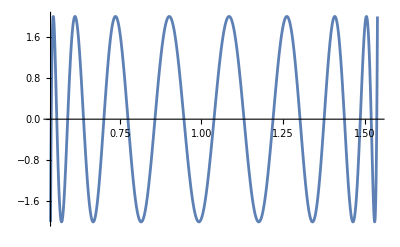

```mathematica
Plot[Tnab[17,a,b,r],{r,ri,ro}]
```

```mathematica
ro
```

1.53846

```mathematica
1/r D[1/r D[ ff[r],r],r]//Simplify
```

(-ff'[r]+r ff''[r])/r^3

```mathematica
1/r D[1/r ff[r],r]//Simplify
```

(-ff[r]+r ff'[r])/r^3

```mathematica
(r^4 1/r D[-(1/r^2 D[r^2 D[f[r],r],r]-(l(l+1))/r^2 f[r])g[r],r]//Simplify)/.{f[r]->f,f'[r]->d1f,f''[r]->d2f,Derivative[3][f][r]->d3f,g[r]->tB,g'[r]->d1B}
```

-f l (1+l) (-d1B r+2 tB)+r (-d1B r (2 d1f+d2f r)+(d1f (2+l+l^2)-r (2 d2f+d3f r)) tB)

```mathematica
(r^4 1/r D[-(1/r^2 D[r^2 D[g[r],r],r]-(l(l+1))/r^2 g[r])f[r],r]//Simplify)/.{f[r]->f,f'[r]->d1f,f''[r]->d2f,Derivative[3][f][r]->d3f,g[r]->tB,g'[r]->td1B,g''[r]->td2B,Derivative[3][g][r]->td3B}
```

d1f r (l (1+l) tB-r (2 td1B+r td2B))+f (-2 l (1+l) tB+r ((2+l+l^2) td1B-r (2 td2B+r td3B)))

```mathematica
r^4 g[r]/r^2 D[r(-1/r^2 D[r^2 D[f[r],r],r]+(l(l+1))/r^2 f[r]),r]//Simplify
```

-g[r] (l (1+l) f[r]+r (-l (1+l) f'[r]+r (3 f''[r]+r f^(3)[r])))

```mathematica
r^4(-1/r^2 D[r^2 D[f[r],r],r]+(l(l+1))/r^2 f[r])/r^2 D[r g[r],r]//Simplify
```

-((g[r]+r g'[r]) (-l (1+l) f[r]+r (2 f'[r]+r f''[r])))

```mathematica
(r^4 1/r f[r](-1/r^2 D[r^2 D[g[r],r],r]+(l(l+1))/r^2 g[r])//Simplify)/.{f[r]->f,f'[r]->d1f,f''[r]->d2f,Derivative[3][f][r]->d3f,g[r]->tB,g'[r]->td1B,g''[r]->td2B,Derivative[3][g][r]->td3B}
```

-f r (-l (1+l) tB+r (2 td1B+r td2B))

```mathematica
(r^4 1/r(-1/r^2 D[r^2 D[f[r],r],r]+(l(l+1))/r^2 f[r])g[r]//Simplify)/.{f[r]->f,f'[r]->d1f,f''[r]->d2f,Derivative[3][f][r]->d3f,g[r]->tB,g'[r]->td1B,g''[r]->td2B,Derivative[3][g][r]->td3B}
```

-r (-f l (1+l)+r (2 d1f+d2f r)) tB

```mathematica
la = 8; lb = 1; lg=9;
ma=0;mb=0;mg=0;
-(lg*(lg+1))(la(la+1)+ lb(lb+1)-lg(lg+1))/2 Integrate[SphericalHarmonicY[la,ma,θ,ϕ]SphericalHarmonicY[lb,mb,θ,ϕ]Conjugate[SphericalHarmonicY[lg,mg,θ,ϕ]]Sin[θ],{θ,0,π},{ϕ,0,2π}]//N

(lb(lb+1))(lb(lb+1)- la(la+1)-lg(lg+1))/2 Integrate[SphericalHarmonicY[la,ma,θ,ϕ]SphericalHarmonicY[lb,mb,θ,ϕ]Conjugate[SphericalHarmonicY[lg,mg,θ,ϕ]]Sin[θ],{θ,0,π},{ϕ,0,2π}]//N
```

176.169

-39.1487

```mathematica
√(((2la+1)(2lb+1)(2lg+1))/(4π))ThreeJSymbol[{la,ma},{lb,mb},{lg,-mg}]ThreeJSymbol[{la,0},{lb,0},{lg,-0}]//N
Integrate[SphericalHarmonicY[la,0,θ,ϕ]SphericalHarmonicY[lb,0,θ,ϕ]Conjugate[SphericalHarmonicY[lg,0,θ,ϕ]]Sin[θ],{θ,0,π},{ϕ,0,2π}]//N
```

0.244679

0.244679

```mathematica
la = 4; lb = 1; lg=4;
ma=-1;mb=1;mg=0;
s1=-ⅈ/2 √(((2la+1)(2lb+1)(2lg+1))/(4π))ThreeJSymbol[{la,ma},{lb,mb},{lg,-mg}]ThreeJSymbol[{la,0},{lb+1,0},{lg,-0}] √((la+lb+lg+2)(la+lb-lg+1)(lb+lg-la+1)(la+lg-lb))//N
s2=-1^(ma+mb-mg)Integrate[(D[SphericalHarmonicY[la,ma,θ,ϕ],θ]D[SphericalHarmonicY[lb,mb,θ,ϕ],ϕ]-D[SphericalHarmonicY[la,ma,θ,ϕ],ϕ]D[SphericalHarmonicY[lb,mb,θ,ϕ],θ])Conjugate[SphericalHarmonicY[lg,mg,θ,ϕ]],{θ,0,π},{ϕ,0,2π}]//N

s1 √(4π)
s2 √(4π)
```

0.+1.5451 ⅈ

0.+1.5451 ⅈ

0.+5.47723 ⅈ

0.+5.47723 ⅈ